# Лабораторная работа 15

```mathematica
Outer[#1{Cos[#2],Sin[#2]}&,Range[0,1,.2],Range[0,2π,π/4]]//MatrixForm
```

((0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.)
(0.2
0.) | (0.141421
0.141421) | (0.
0.2) | (-0.141421
0.141421) | (-0.2
0.) | (-0.141421
-0.141421) | (0.
-0.2) | (0.141421
-0.141421) | (0.2
0.)
(0.4
0.) | (0.282843
0.282843) | (0.
0.4) | (-0.282843
0.282843) | (-0.4
0.) | (-0.282843
-0.282843) | (0.
-0.4) | (0.282843
-0.282843) | (0.4
0.)
(0.6
0.) | (0.424264
0.424264) | (0.
0.6) | (-0.424264
0.424264) | (-0.6
0.) | (-0.424264
-0.424264) | (0.
-0.6) | (0.424264
-0.424264) | (0.6
0.)
(0.8
0.) | (0.565685
0.565685) | (0.
0.8) | (-0.565685
0.565685) | (-0.8
0.) | (-0.565685
-0.565685) | (0.
-0.8) | (0.565685
-0.565685) | (0.8
0.)
(1.
0.) | (0.707107
0.707107) | (0.
1.) | (-0.707107
0.707107) | (-1.
0.) | (-0.707107
-0.707107) | (0.
-1.) | (0.707107
-0.707107) | (1.
0.))

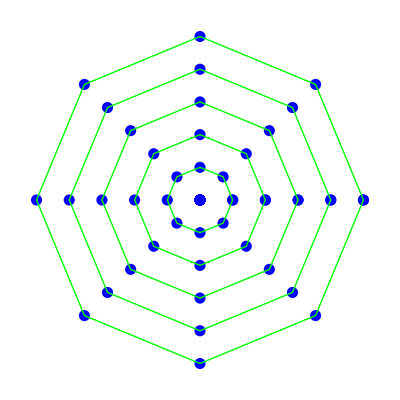

```mathematica
Graphics[{{Hue[2/3],PointSize[.02],Map[Point,#1,{2}]},{Hue[1/3],Line/@#1}}&[Outer[#1{Cos[#2],Sin[#2]}&,Range[0,1,.2],Range[0,2π,π/4]]]]
```

```mathematica
PolarMesh[r_,{nr_,nϕ_}]:=({{Hue[2/3],PointSize[.02],Map[Point,#1,{2}]},{Hue[1/3],Line/@#1}})&[Table[ρ{Cos[ϕ],Sin[ϕ]},{ρ,0,r,r/nr},{ϕ,0,2π,(2π)/nϕ}]]
```

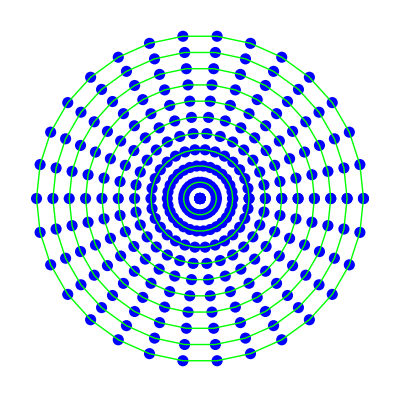

```mathematica
Graphics[PolarMesh[1,{10,30}]]
```

```mathematica
M=Table[x+ⅈ y,{x,0,1,.2},{y,0,1,.2}]
```

{{0.+0. ⅈ,0.+0.2 ⅈ,0.+0.4 ⅈ,0.+0.6 ⅈ,0.+0.8 ⅈ,0.+1. ⅈ},{0.2+0. ⅈ,0.2+0.2 ⅈ,0.2+0.4 ⅈ,0.2+0.6 ⅈ,0.2+0.8 ⅈ,0.2+1. ⅈ},{0.4+0. ⅈ,0.4+0.2 ⅈ,0.4+0.4 ⅈ,0.4+0.6 ⅈ,0.4+0.8 ⅈ,0.4+1. ⅈ},{0.6+0. ⅈ,0.6+0.2 ⅈ,0.6+0.4 ⅈ,0.6+0.6 ⅈ,0.6+0.8 ⅈ,0.6+1. ⅈ},{0.8+0. ⅈ,0.8+0.2 ⅈ,0.8+0.4 ⅈ,0.8+0.6 ⅈ,0.8+0.8 ⅈ,0.8+1. ⅈ},{1.+0. ⅈ,1.+0.2 ⅈ,1.+0.4 ⅈ,1.+0.6 ⅈ,1.+0.8 ⅈ,1.+1. ⅈ}}

```mathematica
z1=Map[{Re@#,Im@#}&,M,{2}]
```

{{{0.,0.},{0.,0.2},{0.,0.4},{0.,0.6},{0.,0.8},{0.,1.}},{{0.2,0.},{0.2,0.2},{0.2,0.4},{0.2,0.6},{0.2,0.8},{0.2,1.}},{{0.4,0.},{0.4,0.2},{0.4,0.4},{0.4,0.6},{0.4,0.8},{0.4,1.}},{{0.6,0.},{0.6,0.2},{0.6,0.4},{0.6,0.6},{0.6,0.8},{0.6,1.}},{{0.8,0.},{0.8,0.2},{0.8,0.4},{0.8,0.6},{0.8,0.8},{0.8,1.}},{{1.,0.},{1.,0.2},{1.,0.4},{1.,0.6},{1.,0.8},{1.,1.}}}

```mathematica
Graphics[{Hue[.3],Line[#]}&/@z1];
```

```mathematica
Graphics[{Hue[.3],Line[#]}&/@Transpose[z1]];
```

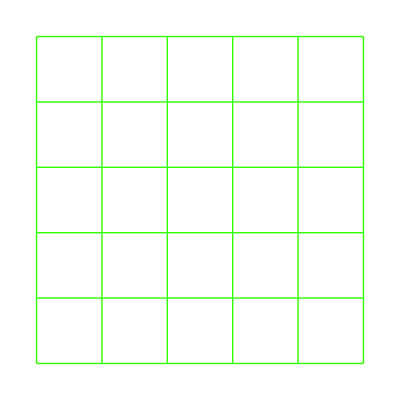

```mathematica
Graphics[{{Hue[.3],Line[#]}&/@#,{Hue[.3],Line[#]}&/@Transpose[#]}&@Map[{Re@#,Im@#}&,Table[x+ⅈ y,{x,0,1,.2},{y,0,1,.2}],{2}]]
```

```mathematica
SquareGrid[{z0_,z1_},{n0_,n1_}]:=Graphics[{{Hue[.3],Line[#]}&/@#,{Hue[.3],Line[#]}&/@Transpose[#]}&@Map[{Re@#,Im@#}&,Table[((n0-i0)Re@z0+i0 Re@z1)/n0+ⅈ((n1-i1)Im@z0+i1 Im@z1)/n1,{i0,0,n0},{i1,0,n1}],{2}]]
```

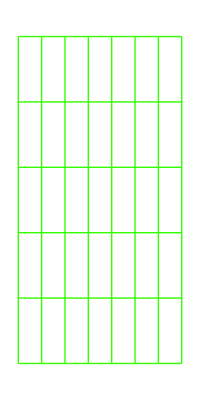

```mathematica
SquareGrid[{1+5ⅈ,-2-ⅈ},{7,5}]
```

```mathematica
CartezianMesh[{z0_,z1_},{n0_,n1_}]:=Module[{N},{N=Length[#]; 
MapIndexed[{Hue[((N-#2⟦1⟧)4/6+#2⟦1⟧3/6)/N],Line[#1]}&,#],MapIndexed[{Hue[((N-#2⟦1⟧)4/6+#2⟦1⟧3/6)/N],Line[#1]}&,#//Transpose]}&@Map[{Re@#,Im@#}&,Table[((n0-i0)Re@z0+i0 Re@z1)/n0+ⅈ((n1-i1)Im@z0+i1 Im@z1)/n1,{i0,0,n0},{i1,0,n1}],{2}]]
```

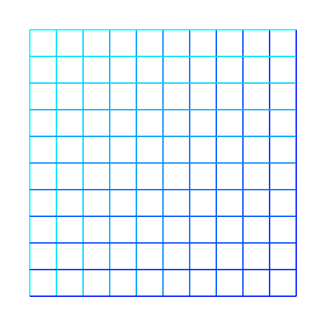

```mathematica
Graphics[CartezianMesh[{1,ⅈ},{10,10}]]
```

```mathematica
R2C[{x_,y_}]:=x+ⅈ y;
```

```mathematica
C2R[z_]:={Re@z,Im@z};
```

```mathematica
TaskSubs[zz_Graphics,f_]:=zz/.{Point[P_]:>(P//R2C//f//C2R//Point),(h:Line|Polygon)[P_]:>h[(#//R2C//f//C2R)&/@P]};
```

```mathematica
ClearAll[ShowConform];
```

```mathematica
ShowConform[f_,g_Graphics,opts___]:=GraphicsGrid[{{g,TaskSubs[g,f]}},opts]
```

```mathematica
zz=Table[r{Cos[ϕ],Sin[ϕ]},{r,0,1,0.2},{ϕ,0,π/2,π/20}];
```

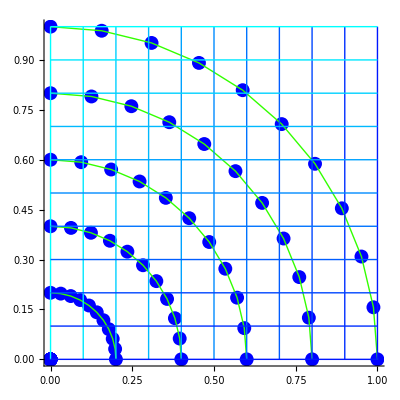

```mathematica
grzz=Graphics[{({{Hue[2/3],PointSize[.025],Map[Point,#,{2}]},{Hue[0.3],Map[Line,#,{1}]}}&)[zz],CartezianMesh[{1,ⅈ},{10,10}]},AspectRatio->Automatic,Axes-> True]
```

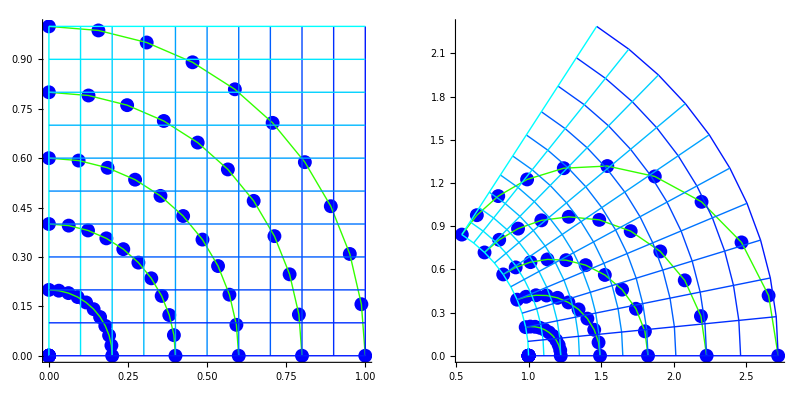

```mathematica
ShowConform[ⅇ^#&,grzz,ImageSize-> 800,PlotLabel-> (z->ⅇ^z)]
```